Authors: Seth Asante, Bianca Dittrich, Jose Padua Arguelles, 
Notebook for paper “Effective spin foams for Lorentzian Quantum Gravity”, arxiv: 2104.00485
This notebook computes expectation values for a triangulation with an inner triangle. The boundary data are 
such that this inner triangle is time-like. The triangulation is described in the paper in section VI C.

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[as,bs,cs,ds,aBlkSq,aBdry1Sq,aBdry2Sq,aBdry3Sq,aBlkSqp,aBdry1Sqp,aBdry2Sqp,γ]
```

```mathematica
Now
```

Sun 27 Jun 2021 22:24:30GMT-4

# Simplicial Geometry

## General

## Cayley Menger

This defines the squared volumes for 4-simplices, tetrahedra and triangles using the Cayley-Menger determinant formulae.  Squared volumes for time-like simplices (satisfying generalized triangle inequalities) are negative, squared volumes for space-like simplices are positive.

The formulas are defined as functions of edge length square(lijSq).

### 4D

```mathematica
CM4D[l12Sq_,l13Sq_,l14Sq_,l15Sq_,l23Sq_,l24Sq_,l25Sq_,l34Sq_,l35Sq_,l45Sq_]:=({{0, l12Sq, l13Sq, l14Sq, l15Sq, 1}, {l12Sq, 0, l23Sq, l24Sq, l25Sq, 1}, {l13Sq, l23Sq, 0, l34Sq, l35Sq, 1}, {l14Sq, l24Sq, l34Sq, 0, l45Sq, 1}, {l15Sq, l25Sq, l35Sq, l45Sq, 0, 1}, {1, 1, 1, 1, 1, 0}})
```

```mathematica
V4Sq[l12Sq_,l13Sq_,l14Sq_,l15Sq_,l23Sq_,l24Sq_,l25Sq_,l34Sq_,l35Sq_,l45Sq_]:=-(-1)^4/(2^4(4!)^2)Det@CM4D[l12Sq,l13Sq,l14Sq,l15Sq,l23Sq,l24Sq,l25Sq,l34Sq,l35Sq,l45Sq]
```

### 3D

```mathematica
CM3D[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:=({{0, l12Sq, l13Sq, l14Sq, 1}, {l12Sq, 0, l23Sq, l24Sq, 1}, {l13Sq, l23Sq, 0, l34Sq, 1}, {l14Sq, l24Sq, l34Sq, 0, 1}, {1, 1, 1, 1, 0}})
```

```mathematica
V3Sq[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:=-(-1)^3/(2^3(3!)^2)Det@CM3D[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq]
```

### 2D

```mathematica
CM2D[l12Sq_,l13Sq_,l23Sq_]:=({{0, l12Sq, l13Sq, 1}, {l12Sq, 0, l23Sq, 1}, {l13Sq, l23Sq, 0, 1}, {1, 1, 1, 0}})
```

```mathematica
V2Sq[l12Sq_,l13Sq_,l23Sq_]:=-(-1)^2/(2^2(2!)^2)Det@CM2D[l12Sq,l13Sq,l23Sq]
```

## Spacelike?

This test whether triangles or tetrahedra are spacelike. A spacelike triangle has all length squared positive and positive volume squared (this implements the usual triangle inequality).  A space-like tetrahedron has only space-like triangles (and therefore edges), and its volume squared is positive.

### 2D

```mathematica
SpacelikeQ[l12Sq_,l13Sq_,l23Sq_]:={l12Sq,l13Sq,l23Sq,V2Sq[l12Sq,l13Sq,l23Sq]}∈PositiveReals
```

### 3D

```mathematica
SpacelikeQ[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:=((SpacelikeQ[l12Sq,l13Sq,l23Sq]&&SpacelikeQ[l12Sq,l14Sq,l24Sq]&&SpacelikeQ[l13Sq,l14Sq,l34Sq]&&SpacelikeQ[l23Sq,l34Sq,l24Sq]))&&Det@CM3D[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq]>0
```

## Realizability

## Inequalities

This asks whether volume squares are positive or negative. Note there is a sign (-1)^n  between the Cayley-Menger determinant  and the Volume formula.

### 2D

```mathematica
Ineq2DQ[l12Sq_,l13Sq_,l23Sq_]:=
Module[{CMDet=Det@CM2D[l12Sq,l13Sq,l23Sq]},
If[SpacelikeQ[l12Sq,l13Sq,l23Sq],
CMDet<0,
CMDet>0]
]
```

### 3D

```mathematica
Ineq3DQ[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:=
Module[{CMDet=Det@CM3D[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq]},
If[SpacelikeQ[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq],
CMDet>0,
CMDet<0]
]
```

### 4D

```mathematica
Ineq4DQ[l12Sq_,l13Sq_,l14Sq_,l15Sq_,l23Sq_,l24Sq_,l25Sq_,l34Sq_,l35Sq_,l45Sq_]:=Det@CM4D[l12Sq,l13Sq,l14Sq,l15Sq,l23Sq,l24Sq,l25Sq,l34Sq,l35Sq,l45Sq]>0
```

## Realizability tests

This implements the triangle inequalities.  E.g. if a tetrahedron includes a time-like triangle, the tetrahedron has itself to be time-like (or null), and therefore has negative 3-Volume.

### 3D

```mathematica
sSimplicesFSplx[#,1]&/@sSimplicesFSplx[{1,2,3,4},2]
```

sSimplicesFSplx[sSimplicesFSplx[{1,2,3,4},1],sSimplicesFSplx[2,1]]

```mathematica
Realizable3DQ[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:=
((Ineq2DQ[l12Sq,l13Sq,l23Sq]&&Ineq2DQ[l12Sq,l14Sq,l24Sq]&&Ineq2DQ[l13Sq,l14Sq,l34Sq]&&Ineq2DQ[l23Sq,l24Sq,l34Sq]))&&Ineq3DQ[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq]
```

### 4D

```mathematica
sSimplicesFSplx[#,1]&/@sSimplicesFSplx[{1,2,3,4,5},3]
```

sSimplicesFSplx[sSimplicesFSplx[{1,2,3,4,5},1],sSimplicesFSplx[3,1]]

```mathematica
Realizable4DQ[l12Sq_,l13Sq_,l14Sq_,l15Sq_,l23Sq_,l24Sq_,l25Sq_,l34Sq_,l35Sq_,l45Sq_]:=
((Realizable3DQ[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq]&&Realizable3DQ[l12Sq,l13Sq,l15Sq,l23Sq,l25Sq,l35Sq]&&Realizable3DQ[l12Sq,l14Sq,l15Sq,l24Sq,l25Sq,l45Sq]&&Realizable3DQ[l13Sq,l14Sq,l15Sq,l34Sq,l35Sq,l45Sq]&&Realizable3DQ[l23Sq,l24Sq,l25Sq,l34Sq,l35Sq,l45Sq]))&&Ineq4DQ[l12Sq,l13Sq,l14Sq,l15Sq,l23Sq,l24Sq,l25Sq,l34Sq,l35Sq,l45Sq]
```

## Angles

This defines the angles in the various simplices.  Euclidean angles apply to space-like triangles, Lorentzian angles to time-like triangles.  To compute the dihedral angle in a 4-simplex at a given triangle t, we can project the simplex to the space orthogonal to this triangle t. This results in a projected triangle t’, with one vertex v of this triangle representing the projected out triangle t. The dihedral angle is then the angle in this triangle t’ at v. The angle is Euclidean is t’ is space-like and Lorentzian if t’ is time-like.

## Euclidean Angles

### 2D

Computes the angle at the vertex 1 in triangle e12,e13,e23. 
The quotient term inside of the ArcCos is the inner product between the normal vectors of edges e12 and e13  at vertex 1 expressed as functions of lengths squared.

```mathematica
θ2DE[l12Sq_,l13Sq_,l23Sq_]:=ArcCos[(-l23Sq+l12Sq+l13Sq)/(2Sqrt[l12Sq l13Sq])]
```

### 3D

Compute the dihedral angle at edge e12. 
Note: the position of the length squared variables in the function matters.

```mathematica
θ3DE[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:=
ArcCos[(-l12Sq^2-(l13Sq-l23Sq) (l14Sq-l24Sq)+l12Sq (l13Sq+l14Sq+l23Sq+l24Sq-2 l34Sq))/(√((l12Sq^2+(l13Sq-l23Sq)^2-2 l12Sq (l13Sq+l23Sq)) (l12Sq^2+(l14Sq-l24Sq)^2-2 l12Sq (l14Sq+l24Sq))))]
(*12 is the "dihedral segment" and 34 its opposed one*)
```

## Lorentzian Angles

### 2D

This defines the Lorentzian angles for the various cases of space-like/ time-like edges.
First condition computes angle between two spacelike edges (*SSX*) --X represent the third edge
Second condition computes angle between a spacelike edge and a timelike edge (*STX*) 
Third condition computes angle between a two time-like edges (*TTX*)

```mathematica
θ2DL[l12Sq_,l13Sq_,l23Sq_]:=If[
V2Sq[l12Sq,l13Sq,l23Sq]<0,
If[
l12Sq>0&&l13Sq>0 (*SSX*),
If[ 
l23Sq>0 && √l23Sq ≥√l12Sq+√l13Sq ,
(*Sss*)-ⅈ π-ArcCosh[-(l12Sq+l13Sq-l23Sq)/(2 √(l12Sq l13Sq))],
(*Ssx*)ArcCosh[(l12Sq+l13Sq-l23Sq)/(2 √(l12Sq l13Sq))]
],
If[
(l12Sq>0&&l13Sq<0 )|| (l12Sq<0&&l13Sq>0 ) (*STX*),
ArcSinh[(l12Sq+l13Sq-l23Sq)/(2 √(-l12Sq l13Sq))]-(ⅈ π)/2,
If[
l12Sq<0&&l13Sq<0(*TTX*),
If[
l23Sq<0 && √-l23Sq ≥√-l12Sq+√-l13Sq ,
ArcCosh[-(-l12Sq-l13Sq+l23Sq)/(2 √(l12Sq l13Sq))]-ⅈ π,
-ArcCosh[(-l12Sq-l13Sq+l23Sq)/(2 √(l12Sq l13Sq))]
]
]
]
]
]
```

### 4D

Lorentzian angles can be generalized to higher dimensions using projections to 2D. ( See the paper for more details)
This computes the angle at triangle 123. 
GetΠΔLengths outputs the length of edges of the triangle t’ left after projecting out the triangle 123

```mathematica
GetΠΔLengths[l12Sq_,l13Sq_,l14Sq_,l15Sq_,l23Sq_,l24Sq_,l25Sq_,l34Sq_,l35Sq_,l45Sq_]:={(l13Sq^2 l24Sq+l12Sq^2 l34Sq+l23Sq (l14Sq^2+l14Sq (l23Sq-l24Sq-l34Sq)+l24Sq l34Sq)+l12Sq ((l13Sq-l14Sq) (l23Sq-l24Sq)-(l13Sq+l14Sq+l23Sq+l24Sq) l34Sq+l34Sq^2)-l13Sq (l14Sq (l23Sq+l24Sq-l34Sq)+l24Sq (l23Sq-l24Sq+l34Sq)))/(l12Sq^2+(l13Sq-l23Sq)^2-2 l12Sq (l13Sq+l23Sq)),(l13Sq^2 l25Sq+l12Sq^2 l35Sq+l23Sq (l15Sq^2+l15Sq (l23Sq-l25Sq-l35Sq)+l25Sq l35Sq)+l12Sq ((l13Sq-l15Sq) (l23Sq-l25Sq)-(l13Sq+l15Sq+l23Sq+l25Sq) l35Sq+l35Sq^2)-l13Sq (l15Sq (l23Sq+l25Sq-l35Sq)+l25Sq (l23Sq-l25Sq+l35Sq)))/(l12Sq^2+(l13Sq-l23Sq)^2-2 l12Sq (l13Sq+l23Sq)),(l14Sq^2 l23Sq+l15Sq^2 l23Sq+l13Sq l24Sq^2-2 l13Sq l24Sq l25Sq+l13Sq l25Sq^2-l12Sq l24Sq l34Sq-l13Sq l24Sq l34Sq+l23Sq l24Sq l34Sq+l12Sq l25Sq l34Sq+l13Sq l25Sq l34Sq-l23Sq l25Sq l34Sq+l12Sq l34Sq^2+l12Sq l24Sq l35Sq+l13Sq l24Sq l35Sq-l23Sq l24Sq l35Sq-l12Sq l25Sq l35Sq-l13Sq l25Sq l35Sq+l23Sq l25Sq l35Sq-2 l12Sq l34Sq l35Sq+l12Sq l35Sq^2+l15Sq (l23Sq (l24Sq-l25Sq+l34Sq-l35Sq)+l12Sq (-l24Sq+l25Sq+l34Sq-l35Sq)+l13Sq (l24Sq-l25Sq-l34Sq+l35Sq))+l14Sq ((l12Sq-l13Sq) (l24Sq-l25Sq-l34Sq+l35Sq)+l23Sq (-2 l15Sq-l24Sq+l25Sq-l34Sq+l35Sq))+(l12Sq^2+(l13Sq-l23Sq)^2-2 l12Sq (l13Sq+l23Sq)) l45Sq)/(l12Sq^2+(l13Sq-l23Sq)^2-2 l12Sq (l13Sq+l23Sq))}
```

```mathematica
θ4DL[l12Sq_,l13Sq_,l14Sq_,l15Sq_,l23Sq_,l24Sq_,l25Sq_,l34Sq_,l35Sq_,l45Sq_]:=
Module[{ΠΔ=GetΠΔLengths[l12Sq,l13Sq,l14Sq,l15Sq,l23Sq,l24Sq,l25Sq,l34Sq,l35Sq,l45Sq]},
If[SpacelikeQ@@ΠΔ,
θ2DE@@ΠΔ,
θ2DL@@ΠΔ
]
]
```

```mathematica
θ4DL[VarsΔ_,VarsSplx_]:=θ4DL[VarsΔ[[1]],VarsΔ[[2]],VarsSplx[[1]],VarsSplx[[2]],VarsΔ[[3]],VarsSplx[[3]],VarsSplx[[4]],VarsSplx[[5]],VarsSplx[[6]],VarsSplx[[7]]]
```

# Simplex and Complex Definitions

## Construction of Terms From Vertices

First we write functions that generate subsimplices (sSimplices) from a simplex (Splx) or a simplicial complex (sCplx)

```mathematica
(*Generate all m-subsimplices From a simplex*)
sSimplicesFSplx[splx_,m_]:=Subsets[splx,{m+1}]
```

```mathematica
(*Generate all m-simplices From a set of n-simplices (simplicial complex)*)
sSimplicesFCplx[sCplx_,m_]:=DeleteDuplicates@Flatten[sSimplicesFSplx[#,m]&/@sCplx,1]
```

Now we want to classify boundary and bulk (n-2)-subsimplices

```mathematica
(*We begin by classifying boundary (n-1)-subsimplices (BdryCoSimplices)*)
```

```mathematica
BdryCoSimplices[sCplx_]:=
Module[
{coSimplices=Flatten[sSimplicesFSplx[#,Length@sCplx[[1]]-1-1]&/@sCplx,1]}
(*By not using DeleteDuplicates as above, we have repeated subsimplices if they belong to more than one simplex*),
Select[coSimplices,Count[coSimplices,#]==1&]]
```

```mathematica
(*We now use the previous function to identify the boundary (n-2)-simplices (bones) of a sCplx*)
```

```mathematica
BdryBones[sCplx_]:=sSimplicesFCplx[BdryCoSimplices@sCplx,Length@sCplx[[1]]-1-2]
```

```mathematica
(*Finally, we get the bulk bones*)
```

```mathematica
BlkBones[sCplx_]:=Complement@@{sSimplicesFCplx[sCplx,Length@sCplx[[1]]-3],BdryBones[sCplx]}
```

# Length Regge Action

This defines the simplex action, bulk terms and boundary terms needed to compute the length Regge action for a general complex in 4D.

```mathematica
(*Contribution of each 4-simplex to the 4-simplex part of the length Regge action*)
Splx4DLAction[l12Sq_,l13Sq_,l14Sq_,l15Sq_,l23Sq_,l24Sq_,l25Sq_,l34Sq_,l35Sq_,l45Sq_]:=
-Sqrt[Abs@
{
V2Sq[l12Sq,l13Sq,l23Sq],V2Sq[l12Sq,l14Sq,l24Sq],V2Sq[l12Sq,l15Sq,l25Sq],V2Sq[l13Sq,l14Sq,l34Sq],V2Sq[l13Sq,l15Sq,l35Sq],V2Sq[l14Sq,l15Sq,l45Sq],V2Sq[l23Sq,l24Sq,l34Sq],V2Sq[l23Sq,l25Sq,l35Sq],V2Sq[l24Sq,l25Sq,l45Sq],V2Sq[l34Sq,l35Sq,l45Sq]
}].{
θ4DL[l12Sq,l13Sq,l14Sq,l15Sq,l23Sq,l24Sq,l25Sq,l34Sq,l35Sq,l45Sq],θ4DL[l12Sq,l14Sq,l13Sq,l15Sq,l24Sq,l23Sq,l25Sq,l34Sq,l45Sq,l35Sq],θ4DL[l12Sq,l15Sq,l13Sq,l14Sq,l25Sq,l23Sq,l24Sq,l35Sq,l45Sq,l34Sq],θ4DL[l13Sq,l14Sq,l12Sq,l15Sq,l34Sq,l23Sq,l35Sq,l24Sq,l45Sq,l25Sq],θ4DL[l13Sq,l15Sq,l12Sq,l14Sq,l35Sq,l23Sq,l34Sq,l25Sq,l45Sq,l24Sq],θ4DL[l14Sq,l15Sq,l12Sq,l13Sq,l45Sq,l24Sq,l34Sq,l25Sq,l35Sq,l23Sq],θ4DL[l23Sq,l24Sq,l12Sq,l25Sq,l34Sq,l13Sq,l35Sq,l14Sq,l45Sq,l15Sq],θ4DL[l23Sq,l25Sq,l12Sq,l24Sq,l35Sq,l13Sq,l34Sq,l15Sq,l45Sq,l14Sq],θ4DL[l24Sq,l25Sq,l12Sq,l23Sq,l45Sq,l14Sq,l34Sq,l15Sq,l35Sq,l13Sq],θ4DL[l34Sq,l35Sq,l13Sq,l23Sq,l45Sq,l14Sq,l24Sq,l15Sq,l25Sq,l12Sq]
}
```

```mathematica
(* Compute the Bulk and Boundary contributions from the bones  *)
```

```mathematica
BdryArea[l12Sq_,l13Sq_,l23Sq_,n_:1]:=If[SpacelikeQ[l12Sq,l13Sq,l23Sq],-ⅈ n  π Sqrt@Abs@V2Sq[l12Sq,l13Sq,l23Sq],π  n Sqrt@Abs@V2Sq[l12Sq,l13Sq,l23Sq]]
```

```mathematica
BlkArea[l12Sq_,l13Sq_,l23Sq_]:=If[SpacelikeQ[l12Sq,l13Sq,l23Sq],-2ⅈ π Sqrt@Abs@V2Sq[l12Sq,l13Sq,l23Sq],2π  Sqrt@Abs@V2Sq[l12Sq,l13Sq,l23Sq]]
```

# Triangulation- Example

Here we define the simplicial complex for which we compute the effective spin foam path integral.

## Simplicial Complex

The complex is specified by a list of 4-simplices. Each 4-simplex is given by its list of vertices.

```mathematica
sCplx33={{1,2,3,4,5},{1,2,3,4,6},{1,2,3,5,6}};
```

This defines the area square of the triangle {v1,v2,v3}.

```mathematica
Var[v1_,v2_,v3_]:=V2Sq[Var[v1,v2],Var[v1,v3],Var[v2,v3]]
```

## Symmetry Reduction

We impose that the lengths of certain edges are equal.  (Var[v2,v2] stands for the squared length of the edge between v1,v2.)  In the end we have 5 length parameters.

```mathematica
Clear[as,bs,cs,ds,es];
Var[1,2]=as;
Var[1,3]=Var[2,3]=bs;
Var[1,4]=Var[1,5]=Var[1,6]=Var[2,4]=Var[2,5]=Var[2,6]=cs;
Var[3,4]=Var[3,5]=Var[3,6]=ds;
Var[4,5]=Var[4,6]=Var[5,6]=as;
```

## Reduced Actions

Computes the length Regge action in the reduced length variables.

```mathematica
(* Write a function for the total Bone Action *)
```

```mathematica
(*Total@(BdryAreas@@@(Var@@@#&/@(sSimplicesFSplx[#,1]&/@BlkBones[sCplx33])))*)
```

```mathematica
(*Total@(BdryAreas@@@(Var@@@#&/@(sSimplicesFSplx[#,1]&/@BdryBones[sCplx33])))*)
```

```mathematica
BoneAction33[as_,bs_,cs_,ds_]:=BlkArea[as,bs,bs]+3 BdryArea[as,cs,cs]+6 BdryArea[bs,cs,ds]+6 BdryArea[cs,cs,as,1/2]+3 BdryArea[ds,ds,as,0]
```

```mathematica
(* A function for the total Simplex Action *)
```

```mathematica
(*Var@@@#&/@(sSimplicesFSplx[#,1]&/@sCplx33)//Tally*)
```

```mathematica
Splx4DAction33[as_,bs_,cs_,ds_]:=3Splx4DLAction[as,bs,cs,cs,bs,cs,cs,ds,ds,as]
```

```mathematica
(* Length Regge action for the complex sCplx33 *)
```

```mathematica
LRAction33[as_,bs_,cs_,ds_]:=BoneAction33[as,bs,cs,ds]+ Splx4DAction33[as,bs,cs,ds]
```

## Reduced Realizability

This test the realizibilty (triangle inequalities) for the 4-simplices: now in our reduced set of area variables.

```mathematica
Realizable33Q[as_,bs_,cs_,ds_]:=Realizable4DQ[as,bs,cs,cs,bs,cs,cs,ds,ds,as]
```

```mathematica
Realizable33Q[120.,-10,15,11]
```

False

```mathematica
(* Test *)
```

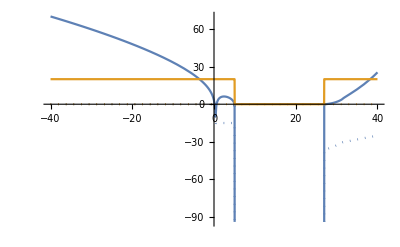

```mathematica
ReImPlot[{LRAction33[20.,bs,15,11],20Boole[Realizable33Q[20.,bs,15,11]]},{bs,-40,40}]
```

## Length-area Inversion

This computes the solution for the lengths in terms of areas.

```mathematica
Simplify@DeleteDuplicates[Var@@@sSimplicesFCplx[sCplx33,2]]
```

{-1/16 as (as-4 bs),-1/16 as (as-4 cs),1/16 (-bs^2-(cs-ds)^2+2 bs (cs+ds)),-1/16 as (as-4 ds)}

```mathematica
Solve[{-1/16 as (as-4 bs),-1/16 as (as-4 cs),-1/16 as (as-4 ds)}=={aBlkSq,aBdry1Sq,aBdry3Sq},{bs,cs,ds}]/.aBdry3Sq->aBdry2Sq
```

{{bs→(16 aBlkSq+as^2)/(4 as),cs→(16 aBdry1Sq+as^2)/(4 as),ds→(16 aBdry2Sq+as^2)/(4 as)}}

The area-length system has four roots. Here we pick  one of the roots. 
We pick the 4th root, other roots will be suppressed by G-functions later.

```mathematica
asF[aBlkSq_,aBdry1Sq_,aBdry2Sq_]:=1/(√3)4 √(-aBdry1Sq+7 aBdry2Sq-aBlkSq+2 √(aBdry1Sq^2+13 aBdry2Sq^2-5 aBdry2Sq aBlkSq+aBlkSq^2-aBdry1Sq (5 aBdry2Sq+aBlkSq)))
```

```mathematica
bsF[aBlkSq_,aBdry1Sq_,aBdry2Sq_]:=(16 aBlkSq+asF[aBlkSq,aBdry1Sq,aBdry2Sq]^2)/(4 asF[aBlkSq,aBdry1Sq,aBdry2Sq])
```

```mathematica
csF[aBlkSq_,aBdry1Sq_,aBdry2Sq_]:=(16 aBdry1Sq+asF[aBlkSq,aBdry1Sq,aBdry2Sq]^2)/(4 asF[aBlkSq,aBdry1Sq,aBdry2Sq])
```

```mathematica
dsF[aBlkSq_,aBdry1Sq_,aBdry2Sq_]:=(16 aBdry2Sq+asF[aBlkSq,aBdry1Sq,aBdry2Sq]^2)/(4 asF[aBlkSq,aBdry1Sq,aBdry2Sq])
```

### Area Regge Action

Compute the area Regge action using the area-length solutions

```mathematica
ARAction33[aBlkSq_,aBdry1Sq_,aBdry2Sq_]:=LRAction33[asF[aBlkSq,aBdry1Sq,aBdry2Sq],bsF[aBlkSq,aBdry1Sq,aBdry2Sq],csF[aBlkSq,aBdry1Sq,aBdry2Sq],dsF[aBlkSq,aBdry1Sq,aBdry2Sq]]
```

### Realizability in Area variables

Compute the realizability conditions in area variables

```mathematica
RealQ[z_]:=Abs@Im@z<10^-10
```

```mathematica
RealArrayQ[array_]:=And@@(RealQ@#&/@array)
```

```mathematica
AreaRealizable33Q[aBlkSq_,aBdry1Sq_,aBdry2Sq_]:=Module[{as=asF[aBlkSq,aBdry1Sq,aBdry2Sq],bs=bsF[aBlkSq,aBdry1Sq,aBdry2Sq],cs=csF[aBlkSq,aBdry1Sq,aBdry2Sq],ds=dsF[aBlkSq,aBdry1Sq,aBdry2Sq]} ,If[RealArrayQ @{as,bs,cs,ds}, Realizable33Q[as,bs,cs,ds],False]]
```

# G functions

This defines the G-functions. There are only non-trivial “Boundary” G-functions (G-functions associated to tetrahedra in the boundary). The G-functions for the bulk tetrahedra evaluate to 1 due to our symmetry reduction. The G-functions also depend on a choice of root for the area-length solutions.
More details about how to define the G-functions can be found in the paper.

```mathematica
(* Inner product function *)
```

```mathematica
P[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:=1/16 (l12Sq^2+(l13Sq-l23Sq) (l14Sq-l24Sq)-l12Sq (l13Sq+l14Sq+l23Sq+l24Sq-2 l34Sq))
```

```mathematica
PTet[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_]:={P[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq],P[l13Sq,l12Sq,l14Sq,l23Sq,l34Sq,l24Sq],P[l14Sq,l12Sq,l13Sq,l24Sq,l34Sq,l23Sq],P[l23Sq,l12Sq,l24Sq,l13Sq,l34Sq,l14Sq],P[l24Sq,l12Sq,l23Sq,l14Sq,l34Sq,l13Sq],P[l34Sq,l13Sq,l23Sq,l14Sq,l24Sq,l12Sq]}
```

```mathematica
(* Constraint between tetrahedra from two simplices *)
```

```mathematica
Constraint[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_,l12Sqp_,l13Sqp_,l14Sqp_,l23Sqp_,l24Sqp_,l34Sqp_]:=1/3 Total[(Abs@(PTet[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq]-PTet[l12Sqp,l13Sqp,l14Sqp,l23Sqp,l24Sqp,l34Sqp]))^2]
```

```mathematica
(* G-factor *)
```

```mathematica
GFacTet[l12Sq_,l13Sq_,l14Sq_,l23Sq_,l24Sq_,l34Sq_,l12Sqp_,l13Sqp_,l14Sqp_,l23Sqp_,l24Sqp_,l34Sqp_,γ_]:=Module[{vs1=V3Sq[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq],vs2=V3Sq[l12Sqp,l13Sqp,l14Sqp,l23Sqp,l24Sqp,l34Sqp]},If[vs1 vs2∈PositiveReals,Exp[-1/(9 γ)Constraint[l12Sq,l13Sq,l14Sq,l23Sq,l24Sq,l34Sq,l12Sqp,l13Sqp,l14Sqp,l23Sqp,l24Sqp,l34Sqp]/(Abs@vs1+Abs@vs2)],0.0]]
```

```mathematica
Tally[Var@@@sSimplicesFSplx[#,1]&/@BdryCoSimplices[sCplx33]]
```

{{{as,cs,cs,cs,cs,as},3},{{bs,cs,cs,ds,ds,as},6}}

Compute the G-factor for the symmetry reduced complex. (Note: The bulk G-factors =1 due to the symmetry)

```mathematica
GBdry33[as_,bs_,cs_,ds_,asp_,bsp_,csp_,dsp_,γ_]:=GFacTet[as,cs,cs,cs,cs,as,asp,csp,csp,csp,csp,asp,γ]^3*GFacTet[bs,cs,cs,ds,ds,as,bsp,csp,csp,dsp,dsp,asp,γ]^6
```

```mathematica
GBdryArea33[aBlkSq_,aBlkSqAbout_,aBdry1Sq_,aBdry2Sq_,γ_]:=Module[{as=asF[aBlkSq,aBdry1Sq,aBdry2Sq],bs=bsF[aBlkSq,aBdry1Sq,aBdry2Sq],cs=csF[aBlkSq,aBdry1Sq,aBdry2Sq],ds=dsF[aBlkSq,aBdry1Sq,aBdry2Sq],asp=asF[aBlkSqAbout,aBdry1Sq,aBdry2Sq],bsp=bsF[aBlkSqAbout,aBdry1Sq,aBdry2Sq],csp=csF[aBlkSqAbout,aBdry1Sq,aBdry2Sq],dsp=dsF[aBlkSqAbout,aBdry1Sq,aBdry2Sq]},GBdry33[as,bs,cs,ds,asp,bsp,csp,dsp,γ]]
```

```mathematica
(* Test Gfactors *)
```

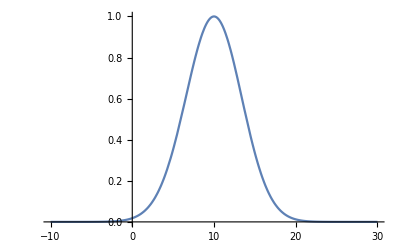

```mathematica
Plot[{GBdryArea33[A,10.,1.,10.,0.1]},{A,-10,30},PlotRange->All]
```

## Deficit angle

We define the deficit angles -- we will compute expectation values of this deficit angles at  triangle123.

```mathematica
(* Note: We consider configuration with a timelike bulk triangle, so ϵ comes with 2Pi term  *)
```

```mathematica
ϵ[as_,bs_,cs_,ds_]:=2Pi - 3 θ4DL[as,bs,cs,cs,bs,cs,cs,ds,ds,as]
```

```mathematica
ϵ[aBlkSq_,aBdry1Sq_,aBdry2Sq_]:=ϵ[asF[aBlkSq,aBdry1Sq,aBdry2Sq],bsF[aBlkSq,aBdry1Sq,aBdry2Sq],csF[aBlkSq,aBdry1Sq,aBdry2Sq],dsF[aBlkSq,aBdry1Sq,aBdry2Sq]]
```

```mathematica
(* Deficit angle in terms of areas *)
```

# Examples

```mathematica
IntegerTest[r_]:=FractionalPart@r<10^-5
```

## Example 1

This sets the values for the boundary areas. There is a scale \lambda, that will be specified later.

```mathematica
{aBdry1Sqp,aBdry2Sqp}:={(50λ)^2 ,-(55λ)^2 };
```

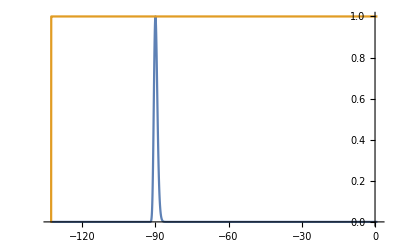

```mathematica
Plot[{GBdryArea33[-A^2,aBlkAboutSq,aBdry1Sqp,aBdry2Sqp,1],Boole@AreaRealizable33Q[-A^2,aBdry1Sqp,aBdry2Sqp]},{A,1,-133λ},PlotRange->All]
```

This sets the value for the bulk area on which the G-functions are peaked.  This value is determined by the full set of boundary data for the triangulation (which not only contain the areas but also sufficient information to determine the lengths in the boundary).

```mathematica
aBlkAboutSq:=-(90λ)^2;
```

#### λ=1

```mathematica
λ=1;
```

This produces a list of  gamma’s, such that boundary areas are integer-valued.

```mathematica
γs=Select[
Table[γ,{γ,0.1,5,0.00001}],
And@@(IntegerTest@#&/@(Sqrt[Abs@{aBdry1Sqp}]/Round[#,10^-5]))&
]
```

{0.1,0.125,0.15625,0.2,0.25,0.3125,0.4,0.5,0.625,0.78125,1.,1.25,1.5625,2.,2.5,3.125,5.}

This shows the range for the bulk areas allowed by triangle inequalities.

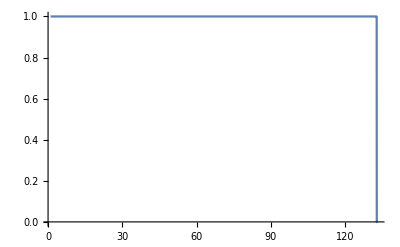

```mathematica
Plot[Boole@AreaRealizable33Q[-nBlk^2,aBdry1Sqp,aBdry2Sqp],{nBlk,1,133λ}]
```

Note: We have just one root, the other roots are suppressed by G-function. 

This defines the various ingredients we need to compute the path integral and expectation values: the deficit angle, the G-function, the action evaluated for the allowed range of bulk areas and for the allowed \gamma’s.

This defines the path integral(s) as a symbolic of \gamma.

```mathematica
ZElements=Sum[{1,nBlk,ϵ[-nBlk^2,aBdry1Sqp,aBdry2Sqp]}(*Boole@AreaRealizable33Q[-nBlk^2,A1sqv,A2sqv]*)Exp[ⅈ Re[ARAction33[-nBlk^2,aBdry1Sqp,aBdry2Sqp]]]GBdryArea33[-nBlk^2,aBlkAboutSq,aBdry1Sqp,aBdry2Sqp,γ],{nBlk,1,132λ}];//Quiet
```

Get the data for the path integral using the allowed values of \gamma.

General::munfl: Exp[-1.42544×10^6+101.002 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.33924×10^6-36.6966 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.21449×10^6+113.987 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

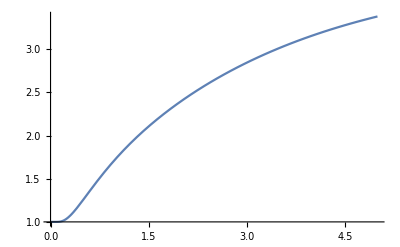

```mathematica
Plot[Abs[ZElements[[1]]],{γ,0,5}]
```

```mathematica
DataZElements=Table[ZElements/.γ->gm,{gm,γs}]//Quiet;
```

```mathematica
{ZPartition,ZElementsArea,ZElementsϵ}=Transpose[DataZElements];
```

Plot of real part of area expectation value (normalized by classical value).

```mathematica
ListPlot[Transpose[{γs,Re[ZElementsArea/ZPartition]/Sqrt[Abs@aBlkAboutSq]}],PlotRange->All]
```

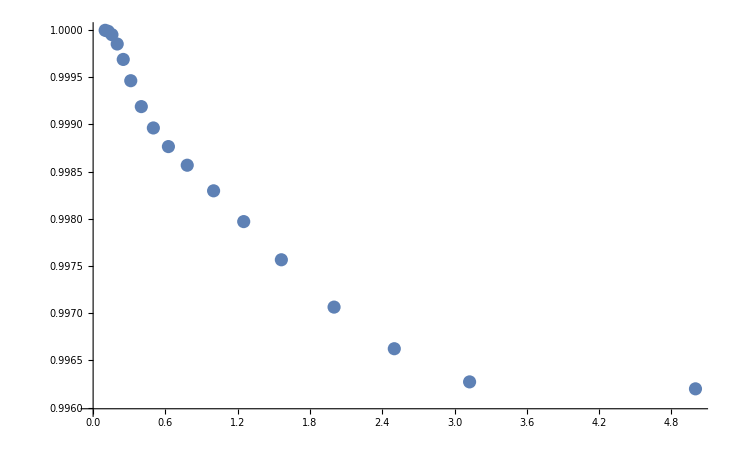

Imaginary part:

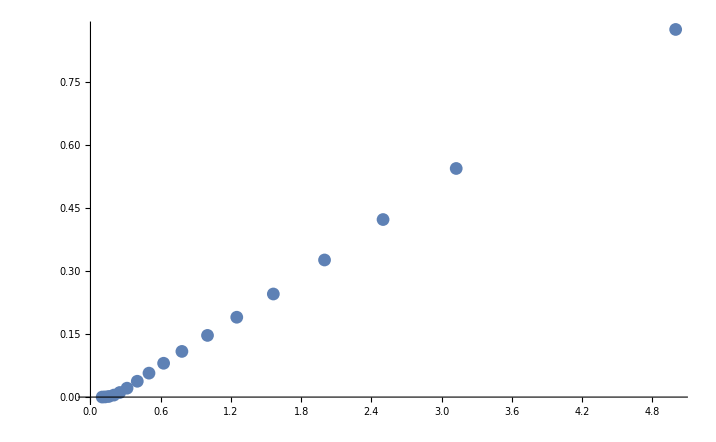

```mathematica
ListPlot[Transpose[{γs,Im[ZElementsArea/ZPartition](*/Sqrt[Abs@aBlkAboutSq]*)}],PlotRange->All]
```

Plot of real part of deficit angle expectation value (normalized by classical value).

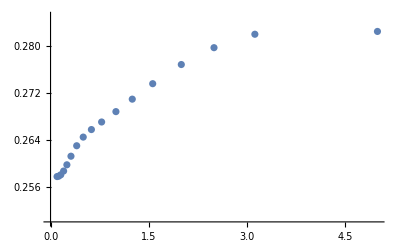

```mathematica
ListPlot[Transpose[{γs,Re[ZElementsϵ/ZPartition]}],PlotRange->{0.25,0.285}]
```

Imaginary part:

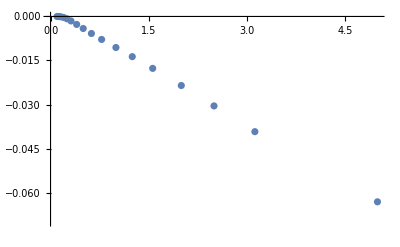

```mathematica
ListPlot[Transpose[{γs,Im[ZElementsϵ/ZPartition]}],PlotRange->{0,-0.07}]
```

```mathematica
Now
```

Sun 27 Jun 2021 22:26:27GMT-4

#### λ=2

```mathematica
λ=2;
```

```mathematica
γs=Select[
Table[γ,{γ,0.1,5,0.00001}],
And@@(IntegerTest@#&/@(Sqrt[Abs@{aBdry1Sqp}]/Round[#,10^-5]))&
]
```

{0.1,0.125,0.15625,0.16,0.2,0.25,0.3125,0.4,0.5,0.625,0.78125,0.8,1.,1.25,1.5625,2.,2.5,3.125,4.,5.}

Note: We have just one root, the other roots are suppressed by G-function. This defines the various ingredients we need to compute the path integral and expectation valuel: the deficit angle, the G-function, the action evaluated for the allowed range of bulk areas and for the allowed \gamma’s.

This defines the arguments in the path integral.

```mathematica
ZElements=Sum[{1,nBlk,ϵ[-nBlk^2,aBdry1Sqp,aBdry2Sqp]}(*Boole@AreaRealizable33Q[-nBlk^2,A1sqv,A2sqv]*)Exp[ⅈ Re[ARAction33[-nBlk^2,aBdry1Sqp,aBdry2Sqp]]]GBdryArea33[-nBlk^2,aBlkAboutSq,aBdry1Sqp,aBdry2Sqp,γ],{nBlk,1,132λ}];//Quiet
```

```mathematica
DataZElements=Table[ZElements/.γ->gm,{gm,γs}]//Quiet;
```

```mathematica
{ZPartition,ZElementsArea,ZElementsϵ}=Transpose[DataZElements];
```

This performs the various summations and computations of expectation values.

Plot of real part of area expectation value (normalized by classical value).

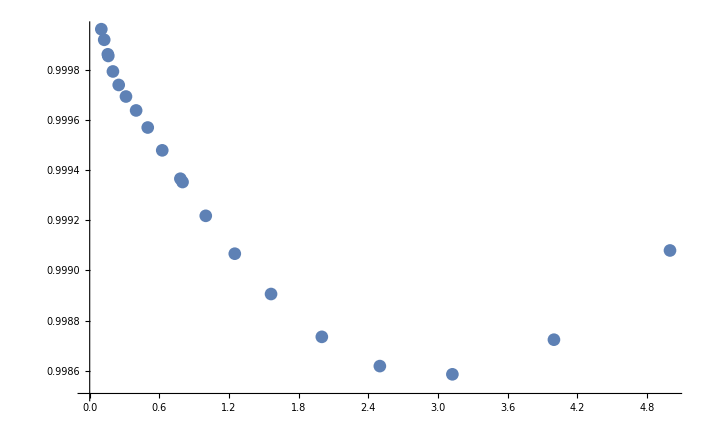

```mathematica
ListPlot[Transpose[{γs,Re[ZElementsArea/ZPartition]/Sqrt[Abs@aBlkAboutSq]}],PlotRange->All]
```

Imaginary part:

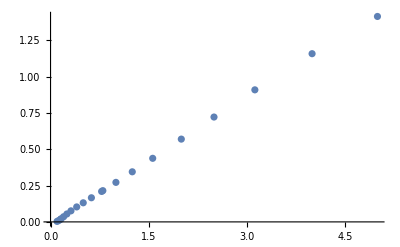

```mathematica
ListPlot[Transpose[{γs,Im[ZElementsArea/ZPartition](*/Sqrt[Abs@aBlkAboutSq]*)}],PlotRange->All]
```

Plot of real part of deficit angle expectation value (normalized by classical value).

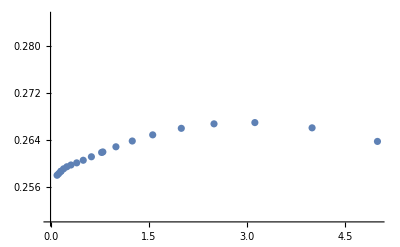

```mathematica
ListPlot[Transpose[{γs,Re[ZElementsϵ/ZPartition]}],PlotRange->{0.25,0.285}]
```

Imaginary part:

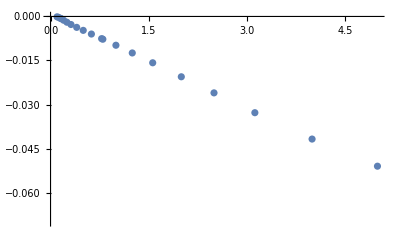

```mathematica
ListPlot[Transpose[{γs,Im[ZElementsϵ/ZPartition]}],PlotRange->{0,-0.07}]
```